```mathematica
ClearAll;
Read in Einstein oscillator potential ab initio data;
(*zrEinsteinmeV=26.329538754361874/1000;cEinsteinmeV=65.1879672429008/1000;*)
(*Carbon and Zironcium mass*)
m={12.0107,91.224,1};
kB=8.6173324*10^-3;
(*Data in*)SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC/4801Ang"];
(*OLD input files :filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_32e00K_energy_displacement_harmonic"};*)
filesEinsteinPot={"C_3200K_energy_displacement","C_3200K_energy_displacement_harmonic","Zr_3200K_energy_displacement","Zr_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
cPlotData=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot[CarbonPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[CarbonPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for C in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
ZirconPotentialEinstein=ReadList[filesEinsteinPot[[3]],{Number, Number}];
zPlotData=ReadList[filesEinsteinPot[[3]],{Number, Number}];
ZirconPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[4]],{Number, Number}];
Show@ListPlot[ZirconPotentialEinstein,PlotLabel->"Anharmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
Show@ListPlot[ZirconPotentialEinsteinHarmonic,PlotLabel->"Harmonic single Einstein oscillator potential for Zr in ZrC",AxesLabel->{"Displacement (Å)","Energy (meV)"}];
```

```mathematica
Define and fit potentials;
(*Carbon*)
V[1,2,x_]:=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
V[1,4,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4},x]
V[1,6,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6},x]
V[1,8,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[1,10,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[1,12,x_]:=Fit[CarbonPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
(*Zirconium*)
V[2,2,x_]:=Fit[ZirconPotentialEinsteinHarmonic,{x^2},x]
V[2,4,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4},x]
V[2,6,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6},x]
V[2,8,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8},x]
V[2,10,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10},x]
V[2,12,x_]:=Fit[ZirconPotentialEinstein,{x^2,x^4,x^6,x^8,x^10,x^12},x]
```

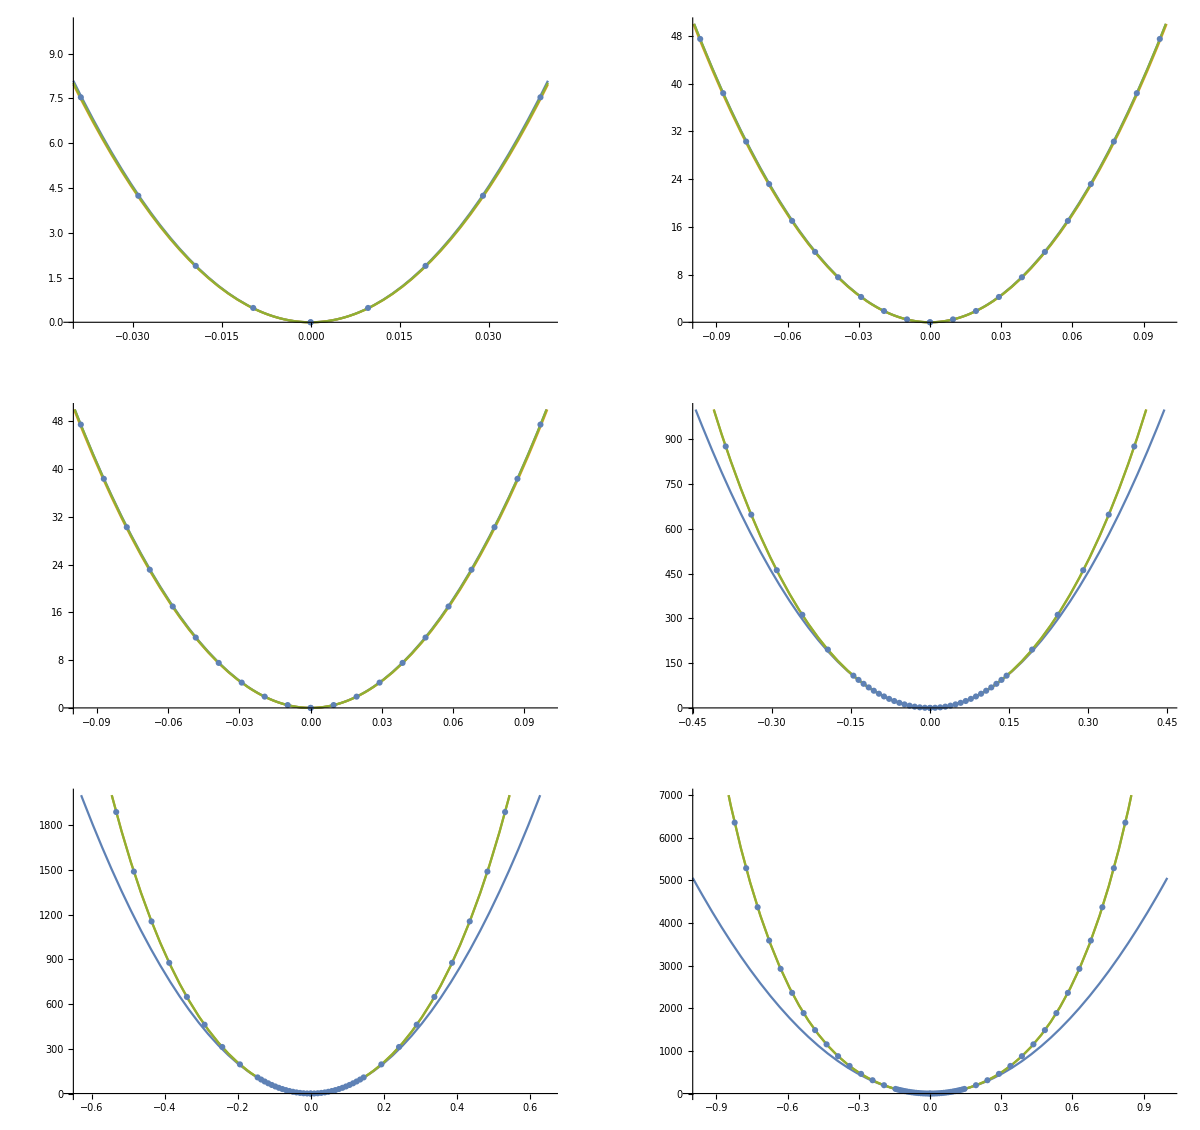

```mathematica
Carbon- look at the fits to examine agreement different length scales;
commonplotinfo={AxesLabel->{"Displacement (Å)","E-E0ref (meV) "}};
P00=With[{B=0.04,H=10},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1=With[{B=0.1,H=50},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2=With[{B=0.45,H=1000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3=With[{B=0.65,H=2000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4=With[{B=1,H=7000},Plot[{Evaluate@V[1,2,x],Evaluate@V[1,6,x],Evaluate@V[1,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00,ListPlot@cPlotData],Show[P0,ListPlot@cPlotData]},{Show[P1,ListPlot@cPlotData],Show[P2,ListPlot@cPlotData]},{Show[P3,ListPlot@cPlotData],Show[P4,ListPlot@cPlotData]}},ImageSize->1200]
```

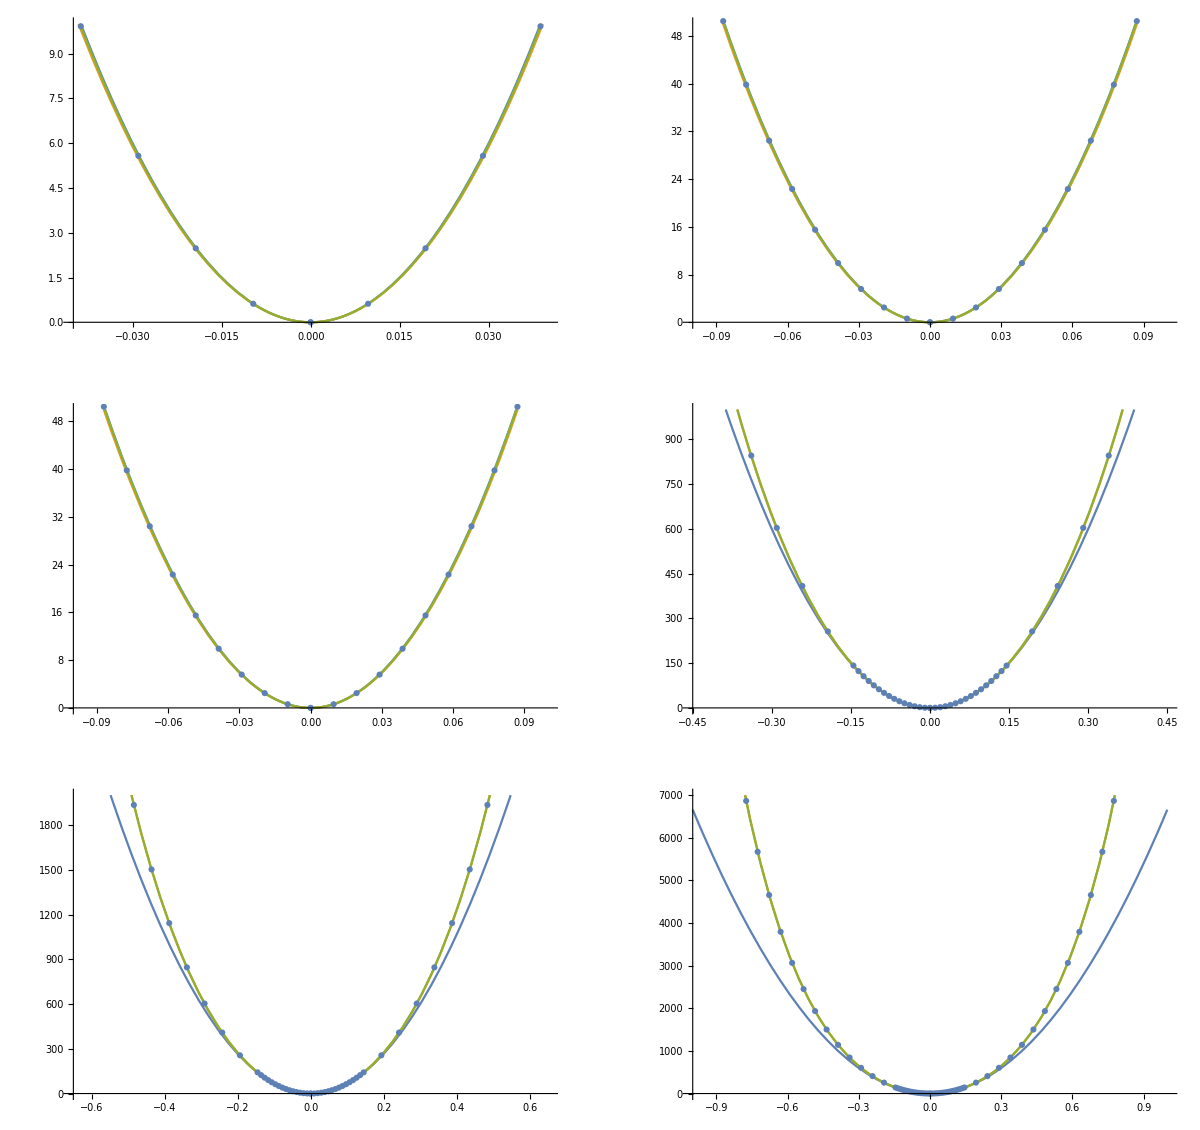

```mathematica
Look at fits at different scales - Zirconium;
P00z=With[{B=0.04,H=10},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P0z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P1z=With[{B=0.1,H=50},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P2z=With[{B=0.45,H=1000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P3z=With[{B=0.65,H=2000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
P4z=With[{B=1,H=7000},Plot[{Evaluate@V[2,2,x],Evaluate@V[2,6,x],Evaluate@V[2,12,x]},{x,-B,B},PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}]];
GraphicsGrid[{{Show[P00z,ListPlot@zPlotData],Show[P0z,ListPlot@zPlotData]},{Show[P1z,ListPlot@zPlotData],Show[P2z,ListPlot@zPlotData]},{Show[P3z,ListPlot@zPlotData],Show[P4z,ListPlot@zPlotData]}},ImageSize->1200]
```

```mathematica
Carbon and zirconium - calculate harmonic frequency of fit (as root of prefactor *2 over mass);
(*If the fitted carbon potential is f(x)=A*x*x, let it be equal to standard harmonic expression, f(x)=A*x*x=1/2*m*omega*omega*x*x*)
"Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Acarbon=V[1,2,x][[1]]
"cOmega0 in meV/Ang**2/AMU is approximately"
cOmega0=Sqrt[2Acarbon/m[[1]]]
"Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is"
Azirconium=V[2,2,x][[1]]
"Z_Omega_0 in meV/Ang**2/AMU is approximately"
zOmega0=Sqrt[2Azirconium/m[[2]]]
```

Carbon harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

5059.19

cOmega0 in meV/Ang**2/AMU is approximately

29.0249

Zr harmonic polynomial fit prefactor 'A' in meV/Ang**2 is

6659.92

Z_Omega_0 in meV/Ang**2/AMU is approximately

12.0836

```mathematica
Carbon and zirconium - calculate eigenvalues and vectors;
(*Find the first 70 eigenvalues and eigenvectors*)
Neigenvalues=70;
(*Define bounds for plotting and solving eigenproblem*)
B=1;H=2000;
(*Carbon Hamiltonians - from harmonic, even symmetry to 12th order*)
ℒall=Table[-(1/(2m[[1]]))*u''[x]+V[1,i,x]*u[x],{i,2,12,2}];
(*Zirconium Hamiltonians - harmonic, even symmetry to 12th order*)
ℒallz=Table[-(1/(2m[[2]]))*u''[x]+V[2,i,x]*u[x],{i,2,12,2}];
(*Carbon eigensystem*)
eigensysC=Table[NDEigensystem[ℒall[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
(*Zironcium eigensystem*)
eigensysZ=Table[NDEigensystem[ℒallz[[j]],u[x],{x,-B,B},Neigenvalues,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0005}}}}],{j,1,6}];
```

```mathematica
(*Carbon and Zironcium eigenenergies*)
(*Indexed like 1 is harmonic, 2 is 4th order ... 6 is 12th order*)
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];
```

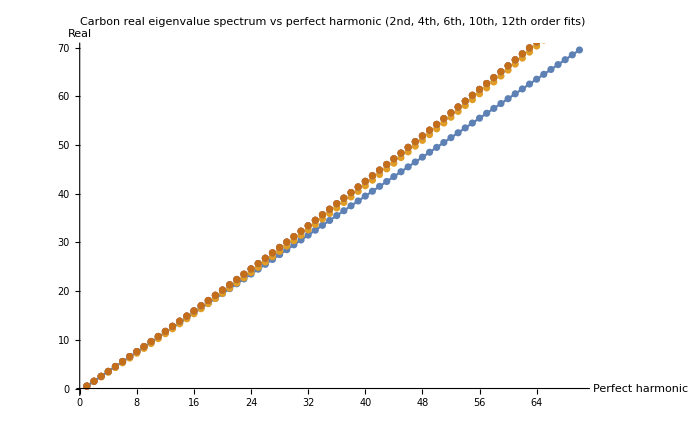

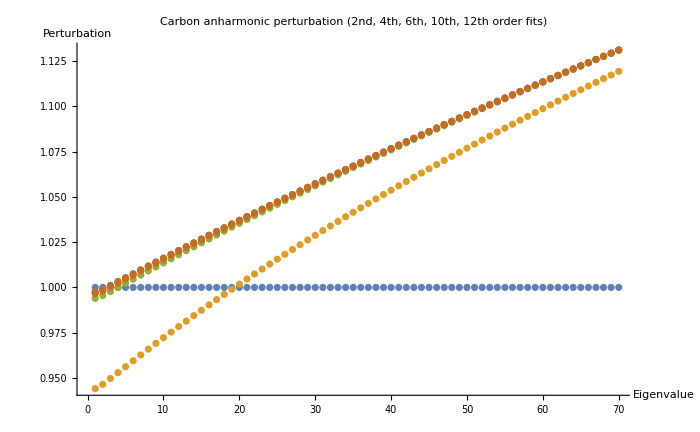

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.472066 | 1.41965 | 2.37407 | 3.33519 | 4.30289 | 5.27703 | 6.25751 | 7.24422 | 8.23704 | 9.23588 | 10.2406 | 11.2512 | 12.2675 | 13.2895 | 14.3171 | 15.3501 | 16.3885 | 17.4323 | 18.4814 | 19.5356 | 20.595 | 21.6594 | 22.7289 | 23.8032 | 24.8825 | 25.9666 | 27.0555 | 28.149 | 29.2473 | 30.3502 | 31.4576 | 32.5695 | 33.686 | 34.8068 | 35.932 | 37.0616 | 38.1955 | 39.3336 | 40.4759 | 41.6224 | 42.7731 | 43.9278 | 45.0866 | 46.2495 | 47.4163 | 48.5871 | 49.7619 | 50.9405 | 52.123 | 53.3093 | 54.4994 | 55.6933 | 56.8909 | 58.0923 | 59.2973 | 60.506 | 61.7183 | 62.9342 | 64.1537 | 65.3768 | 66.6034 | 67.8334 | 69.067 | 70.304 | 71.5444 | 72.7883 | 74.0355 | 75.2861 | 76.5401 | 77.7973
0.496976 | 1.49328 | 2.49428 | 3.49992 | 4.51017 | 5.52497 | 6.5443 | 7.56811 | 8.59636 | 9.62902 | 10.666 | 11.7074 | 12.7531 | 13.803 | 14.8572 | 15.9155 | 16.978 | 18.0447 | 19.1155 | 20.1903 | 21.2692 | 22.3521 | 23.439 | 24.5299 | 25.6247 | 26.7234 | 27.826 | 28.9324 | 30.0427 | 31.1568 | 32.2747 | 33.3963 | 34.5217 | 35.6508 | 36.7836 | 37.9201 | 39.0602 | 40.2039 | 41.3513 | 42.5022 | 43.6568 | 44.8148 | 45.9764 | 47.1415 | 48.3101 | 49.4822 | 50.6577 | 51.8367 | 53.019 | 54.2048 | 55.394 | 56.5865 | 57.7824 | 58.9816 | 60.1842 | 61.39 | 62.5991 | 63.8115 | 65.0272 | 66.2461 | 67.4682 | 68.6935 | 69.9221 | 71.1538 | 72.3887 | 73.6267 | 74.8679 | 76.1122 | 77.3596 | 78.6101
0.498276 | 1.4971 | 2.50044 | 3.50826 | 4.52053 | 5.53721 | 6.55827 | 7.58369 | 8.61341 | 9.64743 | 10.6857 | 11.7282 | 12.7749 | 13.8257 | 14.8807 | 15.9398 | 17.003 | 18.0703 | 19.1415 | 20.2168 | 21.2961 | 22.3793 | 23.4664 | 24.5575 | 25.6524 | 26.7512 | 27.8538 | 28.9603 | 30.0705 | 31.1845 | 32.3022 | 33.4237 | 34.5488 | 35.6777 | 36.8102 | 37.9464 | 39.0862 | 40.2296 | 41.3765 | 42.5271 | 43.6812 | 44.8388 | 46. | 47.1646 | 48.3327 | 49.5043 | 50.6793 | 51.8578 | 53.0396 | 54.2249 | 55.4135 | 56.6055 | 57.8008 | 58.9995 | 60.2014 | 61.4067 | 62.6153 | 63.8271 | 65.0422 | 66.2605 | 67.4821 | 68.7069 | 69.9348 | 71.166 | 72.4003 | 73.6378 | 74.8784 | 76.1222 | 77.3691 | 78.6191
0.498808 | 1.49864 | 2.50288 | 3.51151 | 4.52449 | 5.5418 | 6.56342 | 7.58931 | 8.61945 | 9.65381 | 10.6924 | 11.7351 | 12.782 | 13.833 | 14.8881 | 15.9472 | 17.0104 | 18.0777 | 19.1489 | 20.2241 | 21.3033 | 22.3864 | 23.4734 | 24.5643 | 25.659 | 26.7576 | 27.8601 | 28.9663 | 30.0763 | 31.1901 | 32.3076 | 33.4288 | 34.5537 | 35.6823 | 36.8146 | 37.9505 | 39.0901 | 40.2332 | 41.38 | 42.5303 | 43.6841 | 44.8415 | 46.0024 | 47.1668 | 48.3347 | 49.5061 | 50.6809 | 51.8591 | 53.0407 | 54.2258 | 55.4142 | 56.606 | 57.8012 | 58.9997 | 60.2015 | 61.4066 | 62.615 | 63.8267 | 65.0417 | 66.2599 | 67.4813 | 68.706 | 69.9338 | 71.1649 | 72.3991 | 73.6365 | 74.8771 | 76.1208 | 77.3676 | 78.6175
0.498622 | 1.49811 | 2.50206 | 3.51044 | 4.52322 | 5.54037 | 6.56185 | 7.58765 | 8.61772 | 9.65203 | 10.6906 | 11.7333 | 12.7802 | 13.8312 | 14.8863 | 15.9456 | 17.0088 | 18.0761 | 19.1475 | 20.2227 | 21.302 | 22.3852 | 23.4723 | 24.5633 | 25.6581 | 26.7568 | 27.8594 | 28.9657 | 30.0758 | 31.1896 | 32.3072 | 33.4285 | 34.5536 | 35.6822 | 36.8146 | 37.9506 | 39.0902 | 40.2334 | 41.3802 | 42.5305 | 43.6844 | 44.8419 | 46.0028 | 47.1673 | 48.3352 | 49.5066 | 50.6814 | 51.8596 | 53.0413 | 54.2264 | 55.4148 | 56.6066 | 57.8018 | 59.0003 | 60.2021 | 61.4072 | 62.6156 | 63.8273 | 65.0422 | 66.2604 | 67.4818 | 68.7064 | 69.9343 | 71.1653 | 72.3995 | 73.6369 | 74.8774 | 76.1211 | 77.3678 | 78.6177

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.944131 | 0.946433 | 0.949628 | 0.952912 | 0.956197 | 0.95946 | 0.962694 | 0.965896 | 0.969064 | 0.972198 | 0.975299 | 0.978368 | 0.981404 | 0.984409 | 0.987384 | 0.990329 | 0.993245 | 0.996132 | 0.998992 | 1.00183 | 1.00463 | 1.00741 | 1.01017 | 1.0129 | 1.01561 | 1.0183 | 1.02096 | 1.0236 | 1.02622 | 1.02882 | 1.0314 | 1.03395 | 1.03649 | 1.03901 | 1.04151 | 1.04399 | 1.04645 | 1.0489 | 1.05132 | 1.05373 | 1.05613 | 1.0585 | 1.06086 | 1.06321 | 1.06554 | 1.06785 | 1.07015 | 1.07243 | 1.0747 | 1.07696 | 1.0792 | 1.08142 | 1.08364 | 1.08584 | 1.08802 | 1.0902 | 1.09236 | 1.09451 | 1.09664 | 1.09877 | 1.10088 | 1.10298 | 1.10507 | 1.10715 | 1.10922 | 1.11127 | 1.11332 | 1.11535 | 1.11737 | 1.11939
0.993951 | 0.995522 | 0.997712 | 0.999977 | 1.00226 | 1.00454 | 1.00682 | 1.00908 | 1.01134 | 1.01358 | 1.01581 | 1.01804 | 1.02025 | 1.02244 | 1.02463 | 1.02681 | 1.02897 | 1.03113 | 1.03327 | 1.0354 | 1.03752 | 1.03963 | 1.04173 | 1.04382 | 1.0459 | 1.04798 | 1.05004 | 1.05209 | 1.05413 | 1.05616 | 1.05819 | 1.0602 | 1.06221 | 1.0642 | 1.06619 | 1.06817 | 1.07014 | 1.0721 | 1.07406 | 1.07601 | 1.07794 | 1.07988 | 1.0818 | 1.08371 | 1.08562 | 1.08752 | 1.08941 | 1.0913 | 1.09318 | 1.09505 | 1.09691 | 1.09877 | 1.10062 | 1.10246 | 1.1043 | 1.10613 | 1.10795 | 1.10977 | 1.11158 | 1.11338 | 1.11518 | 1.11697 | 1.11875 | 1.12053 | 1.1223 | 1.12407 | 1.12583 | 1.12759 | 1.12934 | 1.13108
0.996553 | 0.998065 | 1.00017 | 1.00236 | 1.00456 | 1.00677 | 1.00897 | 1.01116 | 1.01334 | 1.01552 | 1.01769 | 1.01984 | 1.02199 | 1.02413 | 1.02626 | 1.02838 | 1.03049 | 1.03259 | 1.03468 | 1.03676 | 1.03883 | 1.0409 | 1.04295 | 1.045 | 1.04704 | 1.04907 | 1.05109 | 1.0531 | 1.0551 | 1.0571 | 1.05909 | 1.06107 | 1.06304 | 1.06501 | 1.06696 | 1.06891 | 1.07085 | 1.07279 | 1.07472 | 1.07664 | 1.07855 | 1.08045 | 1.08235 | 1.08424 | 1.08613 | 1.08801 | 1.08988 | 1.09174 | 1.0936 | 1.09545 | 1.0973 | 1.09914 | 1.10097 | 1.10279 | 1.10461 | 1.10643 | 1.10824 | 1.11004 | 1.11183 | 1.11362 | 1.11541 | 1.11718 | 1.11896 | 1.12072 | 1.12249 | 1.12424 | 1.12599 | 1.12774 | 1.12948 | 1.13121
0.997616 | 0.999091 | 1.00115 | 1.00329 | 1.00544 | 1.0076 | 1.00976 | 1.01191 | 1.01405 | 1.01619 | 1.01832 | 1.02044 | 1.02256 | 1.02466 | 1.02676 | 1.02885 | 1.03093 | 1.03301 | 1.03508 | 1.03713 | 1.03918 | 1.04123 | 1.04326 | 1.04529 | 1.04731 | 1.04932 | 1.05132 | 1.05332 | 1.05531 | 1.05729 | 1.05926 | 1.06123 | 1.06319 | 1.06514 | 1.06709 | 1.06903 | 1.07096 | 1.07289 | 1.0748 | 1.07672 | 1.07862 | 1.08052 | 1.08241 | 1.08429 | 1.08617 | 1.08805 | 1.08991 | 1.09177 | 1.09362 | 1.09547 | 1.09731 | 1.09915 | 1.10097 | 1.1028 | 1.10461 | 1.10643 | 1.10823 | 1.11003 | 1.11182 | 1.11361 | 1.11539 | 1.11717 | 1.11894 | 1.12071 | 1.12247 | 1.12422 | 1.12597 | 1.12771 | 1.12945 | 1.13119
0.997243 | 0.998737 | 1.00082 | 1.00298 | 1.00516 | 1.00734 | 1.00952 | 1.01169 | 1.01385 | 1.016 | 1.01815 | 1.02029 | 1.02241 | 1.02453 | 1.02664 | 1.02875 | 1.03084 | 1.03292 | 1.035 | 1.03706 | 1.03912 | 1.04117 | 1.04321 | 1.04525 | 1.04727 | 1.04929 | 1.0513 | 1.0533 | 1.05529 | 1.05728 | 1.05925 | 1.06122 | 1.06319 | 1.06514 | 1.06709 | 1.06903 | 1.07096 | 1.07289 | 1.07481 | 1.07672 | 1.07863 | 1.08053 | 1.08242 | 1.0843 | 1.08618 | 1.08806 | 1.08992 | 1.09178 | 1.09364 | 1.09548 | 1.09732 | 1.09916 | 1.10099 | 1.10281 | 1.10463 | 1.10644 | 1.10824 | 1.11004 | 1.11183 | 1.11362 | 1.1154 | 1.11718 | 1.11895 | 1.12071 | 1.12247 | 1.12423 | 1.12598 | 1.12772 | 1.12946 | 1.13119

```mathematica
Carbon - look at harmonic and anharmonic eigenvalues;
eigenEnergies=Table[eigensysC[[k]][[1]]/cOmega0,{k,1,6}];
Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Carbon real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergies,ImageSize->700]
Show[ListPlot[relativeEigenval,PlotLabel->"Carbon anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}],ImageSize->700]
relativeEigenval=Table[eigensysC[[k]][[1]]/eigensysC[[1]][[1]],{k,1,6}];
eigenEnergies//TableForm
relativeEigenval//TableForm
```

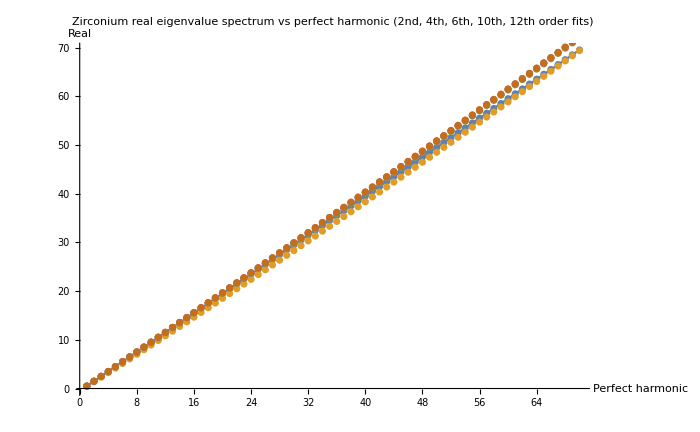

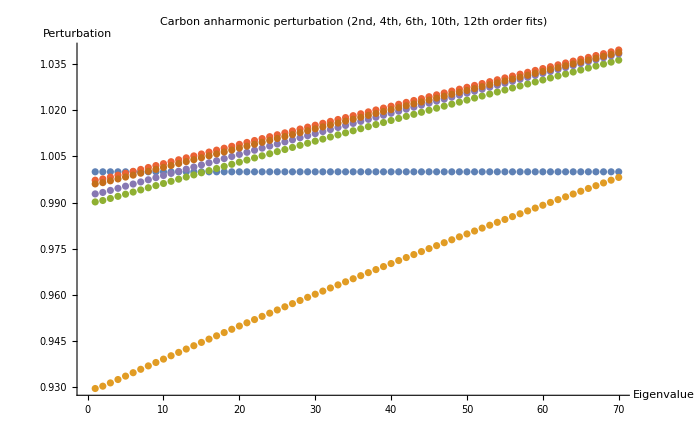

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5 | 15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5 | 30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5 | 45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5 | 60.5 | 61.5 | 62.5 | 63.5 | 64.5 | 65.5 | 66.5 | 67.5 | 68.5 | 69.5
0.464752 | 1.3954 | 2.32831 | 3.26349 | 4.20091 | 5.14055 | 6.08241 | 7.02647 | 7.97271 | 8.92112 | 9.87168 | 10.8244 | 11.7792 | 12.7362 | 13.6952 | 14.6564 | 15.6196 | 16.5849 | 17.5523 | 18.5217 | 19.4931 | 20.4665 | 21.442 | 22.4194 | 23.3988 | 24.3802 | 25.3636 | 26.3489 | 27.3361 | 28.3253 | 29.3164 | 30.3095 | 31.3044 | 32.3012 | 33.2999 | 34.3004 | 35.3029 | 36.3072 | 37.3133 | 38.3212 | 39.331 | 40.3426 | 41.356 | 42.3713 | 43.3883 | 44.4071 | 45.4276 | 46.4499 | 47.474 | 48.4999 | 49.5275 | 50.5568 | 51.5878 | 52.6206 | 53.6551 | 54.6912 | 55.7291 | 56.7687 | 57.8099 | 58.8529 | 59.8975 | 60.9437 | 61.9916 | 63.0412 | 64.0924 | 65.1452 | 66.1997 | 67.2558 | 68.3135 | 69.3728
0.4951 | 1.48601 | 2.47834 | 3.47207 | 4.46722 | 5.46378 | 6.46173 | 7.46109 | 8.46184 | 9.46398 | 10.4675 | 11.4724 | 12.4787 | 13.4864 | 14.4955 | 15.5059 | 16.5177 | 17.5308 | 18.5454 | 19.5613 | 20.5785 | 21.5971 | 22.617 | 23.6383 | 24.661 | 25.6849 | 26.7103 | 27.7369 | 28.7649 | 29.7942 | 30.8248 | 31.8568 | 32.8901 | 33.9247 | 34.9606 | 35.9978 | 37.0364 | 38.0762 | 39.1174 | 40.1598 | 41.2036 | 42.2486 | 43.2949 | 44.3426 | 45.3915 | 46.4417 | 47.4931 | 48.5459 | 49.5999 | 50.6552 | 51.7118 | 52.7697 | 53.8288 | 54.8892 | 55.9508 | 57.0137 | 58.0779 | 59.1433 | 60.2099 | 61.2778 | 62.347 | 63.4174 | 64.489 | 65.5619 | 66.636 | 67.7114 | 68.7879 | 69.8658 | 70.9448 | 72.0251
0.498635 | 1.49654 | 2.49571 | 3.49614 | 4.49784 | 5.5008 | 6.50503 | 7.51051 | 8.51725 | 9.52526 | 10.5345 | 11.545 | 12.5568 | 13.5698 | 14.5841 | 15.5996 | 16.6164 | 17.6344 | 18.6536 | 19.6741 | 20.6959 | 21.7189 | 22.7431 | 23.7686 | 24.7953 | 25.8232 | 26.8524 | 27.8828 | 28.9144 | 29.9473 | 30.9814 | 32.0167 | 33.0533 | 34.0911 | 35.1301 | 36.1703 | 37.2117 | 38.2544 | 39.2983 | 40.3434 | 41.3897 | 42.4372 | 43.4859 | 44.5359 | 45.587 | 46.6394 | 47.693 | 48.7477 | 49.8037 | 50.8609 | 51.9193 | 52.9789 | 54.0397 | 55.1016 | 56.1648 | 57.2292 | 58.2947 | 59.3615 | 60.4294 | 61.4985 | 62.5688 | 63.6403 | 64.713 | 65.7869 | 66.8619 | 67.9381 | 69.0155 | 70.0941 | 71.1738 | 72.2548
0.496408 | 1.48993 | 2.48486 | 3.4812 | 4.47894 | 5.47808 | 6.47861 | 7.48053 | 8.48384 | 9.48852 | 10.4946 | 11.502 | 12.5108 | 13.521 | 14.5325 | 15.5454 | 16.5597 | 17.5752 | 18.5922 | 19.6105 | 20.6301 | 21.651 | 22.6733 | 23.6969 | 24.7219 | 25.7481 | 26.7757 | 27.8046 | 28.8348 | 29.8663 | 30.8991 | 31.9333 | 32.9687 | 34.0054 | 35.0434 | 36.0827 | 37.1233 | 38.1651 | 39.2083 | 40.2527 | 41.2984 | 42.3454 | 43.3936 | 44.4431 | 45.4938 | 46.5459 | 47.5991 | 48.6537 | 49.7095 | 50.7665 | 51.8248 | 52.8843 | 53.945 | 55.007 | 56.0703 | 57.1347 | 58.2004 | 59.2674 | 60.3355 | 61.4049 | 62.4755 | 63.5473 | 64.6203 | 65.6946 | 66.77 | 67.8467 | 68.9245 | 70.0036 | 71.0839 | 72.1653
0.498031 | 1.49472 | 2.49267 | 3.49188 | 4.49235 | 5.49408 | 6.49706 | 7.50131 | 8.50682 | 9.51358 | 10.5216 | 11.5309 | 12.5414 | 13.5532 | 14.5663 | 15.5806 | 16.5962 | 17.613 | 18.6311 | 19.6504 | 20.671 | 21.6928 | 22.7159 | 23.7403 | 24.7659 | 25.7927 | 26.8208 | 27.8501 | 28.8807 | 29.9126 | 30.9456 | 31.98 | 33.0155 | 34.0524 | 35.0904 | 36.1297 | 37.1702 | 38.212 | 39.255 | 40.2993 | 41.3448 | 42.3915 | 43.4394 | 44.4886 | 45.539 | 46.5906 | 47.6435 | 48.6976 | 49.7529 | 50.8094 | 51.8672 | 52.9262 | 53.9863 | 55.0478 | 56.1104 | 57.1742 | 58.2393 | 59.3056 | 60.373 | 61.4417 | 62.5116 | 63.5827 | 64.655 | 65.7285 | 66.8032 | 67.8791 | 68.9562 | 70.0345 | 71.114 | 72.1947

1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.
0.929503 | 0.930264 | 0.931325 | 0.932425 | 0.933535 | 0.934646 | 0.935755 | 0.936862 | 0.937966 | 0.939065 | 0.94016 | 0.941252 | 0.942339 | 0.943421 | 0.9445 | 0.945574 | 0.946644 | 0.94771 | 0.948771 | 0.949828 | 0.950881 | 0.951931 | 0.952976 | 0.954017 | 0.955054 | 0.956087 | 0.957116 | 0.958141 | 0.959163 | 0.960181 | 0.961194 | 0.962205 | 0.963211 | 0.964214 | 0.965214 | 0.966209 | 0.967202 | 0.968191 | 0.969176 | 0.970158 | 0.971136 | 0.972111 | 0.973083 | 0.974052 | 0.975017 | 0.975979 | 0.976938 | 0.977893 | 0.978846 | 0.979795 | 0.980741 | 0.981685 | 0.982625 | 0.983562 | 0.984496 | 0.985427 | 0.986356 | 0.987281 | 0.988204 | 0.989123 | 0.99004 | 0.990954 | 0.991866 | 0.992774 | 0.99368 | 0.994583 | 0.995483 | 0.996381 | 0.997276 | 0.998169
0.9902 | 0.990673 | 0.991334 | 0.992021 | 0.992716 | 0.993414 | 0.994113 | 0.994812 | 0.99551 | 0.996208 | 0.996906 | 0.997603 | 0.998298 | 0.998993 | 0.999687 | 1.00038 | 1.00107 | 1.00176 | 1.00245 | 1.00314 | 1.00383 | 1.00452 | 1.0052 | 1.00589 | 1.00657 | 1.00725 | 1.00793 | 1.00861 | 1.00929 | 1.00997 | 1.01065 | 1.01133 | 1.012 | 1.01268 | 1.01335 | 1.01402 | 1.0147 | 1.01537 | 1.01604 | 1.0167 | 1.01737 | 1.01804 | 1.0187 | 1.01937 | 1.02003 | 1.0207 | 1.02136 | 1.02202 | 1.02268 | 1.02334 | 1.024 | 1.02465 | 1.02531 | 1.02597 | 1.02662 | 1.02727 | 1.02793 | 1.02858 | 1.02923 | 1.02988 | 1.03053 | 1.03118 | 1.03182 | 1.03247 | 1.03312 | 1.03376 | 1.0344 | 1.03505 | 1.03569 | 1.03633
0.99727 | 0.997692 | 0.998283 | 0.998898 | 0.999521 | 1.00015 | 1.00077 | 1.0014 | 1.00203 | 1.00266 | 1.00329 | 1.00392 | 1.00454 | 1.00517 | 1.0058 | 1.00643 | 1.00705 | 1.00768 | 1.0083 | 1.00893 | 1.00956 | 1.01018 | 1.0108 | 1.01143 | 1.01205 | 1.01267 | 1.0133 | 1.01392 | 1.01454 | 1.01516 | 1.01578 | 1.0164 | 1.01702 | 1.01764 | 1.01826 | 1.01888 | 1.0195 | 1.02012 | 1.02073 | 1.02135 | 1.02197 | 1.02258 | 1.0232 | 1.02381 | 1.02443 | 1.02504 | 1.02566 | 1.02627 | 1.02688 | 1.02749 | 1.0281 | 1.02872 | 1.02933 | 1.02994 | 1.03055 | 1.03116 | 1.03176 | 1.03237 | 1.03298 | 1.03359 | 1.0342 | 1.0348 | 1.03541 | 1.03601 | 1.03662 | 1.03722 | 1.03783 | 1.03843 | 1.03903 | 1.03964
0.992816 | 0.993287 | 0.993946 | 0.994629 | 0.995321 | 0.996015 | 0.99671 | 0.997404 | 0.998099 | 0.998792 | 0.999484 | 1.00018 | 1.00087 | 1.00156 | 1.00224 | 1.00293 | 1.00362 | 1.0043 | 1.00498 | 1.00566 | 1.00635 | 1.00702 | 1.0077 | 1.00838 | 1.00906 | 1.00973 | 1.0104 | 1.01108 | 1.01175 | 1.01242 | 1.01309 | 1.01375 | 1.01442 | 1.01509 | 1.01575 | 1.01641 | 1.01708 | 1.01774 | 1.0184 | 1.01906 | 1.01971 | 1.02037 | 1.02103 | 1.02168 | 1.02233 | 1.02299 | 1.02364 | 1.02429 | 1.02494 | 1.02559 | 1.02623 | 1.02688 | 1.02752 | 1.02817 | 1.02881 | 1.02945 | 1.0301 | 1.03074 | 1.03138 | 1.03201 | 1.03265 | 1.03329 | 1.03392 | 1.03456 | 1.03519 | 1.03583 | 1.03646 | 1.03709 | 1.03772 | 1.03835
0.996062 | 0.996481 | 0.997069 | 0.99768 | 0.9983 | 0.998923 | 0.999548 | 1.00017 | 1.0008 | 1.00143 | 1.00206 | 1.00269 | 1.00331 | 1.00394 | 1.00457 | 1.0052 | 1.00583 | 1.00646 | 1.00708 | 1.00771 | 1.00834 | 1.00897 | 1.0096 | 1.01022 | 1.01085 | 1.01148 | 1.01211 | 1.01273 | 1.01336 | 1.01399 | 1.01461 | 1.01524 | 1.01586 | 1.01649 | 1.01711 | 1.01774 | 1.01836 | 1.01899 | 1.01961 | 1.02023 | 1.02086 | 1.02148 | 1.0221 | 1.02273 | 1.02335 | 1.02397 | 1.02459 | 1.02521 | 1.02583 | 1.02645 | 1.02707 | 1.02769 | 1.02831 | 1.02893 | 1.02955 | 1.03017 | 1.03078 | 1.0314 | 1.03202 | 1.03263 | 1.03325 | 1.03386 | 1.03448 | 1.03509 | 1.03571 | 1.03632 | 1.03694 | 1.03755 | 1.03816 | 1.03877

```mathematica
Zirconium - look at harmonic and anharmonic eigenvalues;
(*zOmega=13.44788050977517;M=91;V[x_,M_,Omega_]:=0.5*Omega*Omega*M*x^2*)
eigenEnergiesZ=Table[eigensysZ[[k]][[1]]/zOmega0,{k,1,6}];
Show[Plot[f[x]=x-0.5,{x,1,Neigenvalues},PlotLabel->"Zirconium real eigenvalue spectrum vs perfect harmonic \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Perfect harmonic","Real"}],ListPlot@eigenEnergiesZ,ImageSize->700]
relativeEigenvalz=Table[eigensysZ[[k]][[1]]/eigensysZ[[1]][[1]],{k,1,6}];
Show[ListPlot[relativeEigenvalz,ImageSize->700,PlotLabel->"Carbon anharmonic perturbation \n(2nd, 4th, 6th, 10th, 12th order fits)",AxesLabel->{"Eigenvalue","Perturbation"}]]
eigenEnergiesZ//TableForm
relativeEigenvalz//TableForm
```

{1.,1.11939,1.13108,1.13121,1.13119,1.13119}

{1.,0.998169,1.03633,1.03964,1.03835,1.03877}

{ImageSize→600,PlotLegends→SwatchLegend[{10th eigenvalue,20th eigenvalue,30th eigenvalue,40th eigenvalue,50th eigenvalue,60th eigenvalue,70th eigenvalue}],PlotLabel→Convergence of anharmonic perturbation with fit order,AxesLabel→{1/2 * Fit Order 
(2nd, 4th, 6th, 8th, 10th, 12th),Anharmonic
perturbation}}

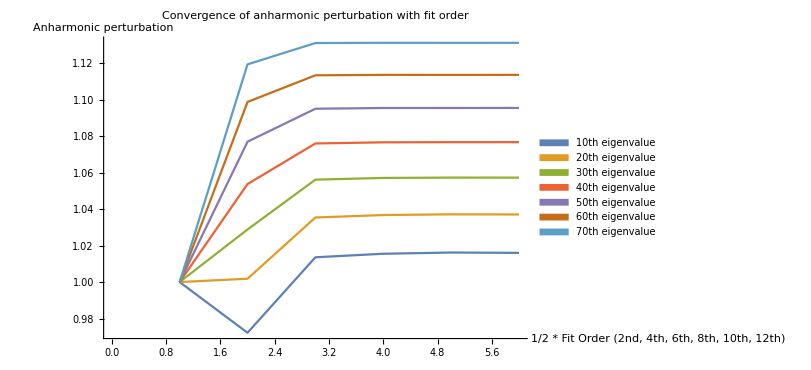

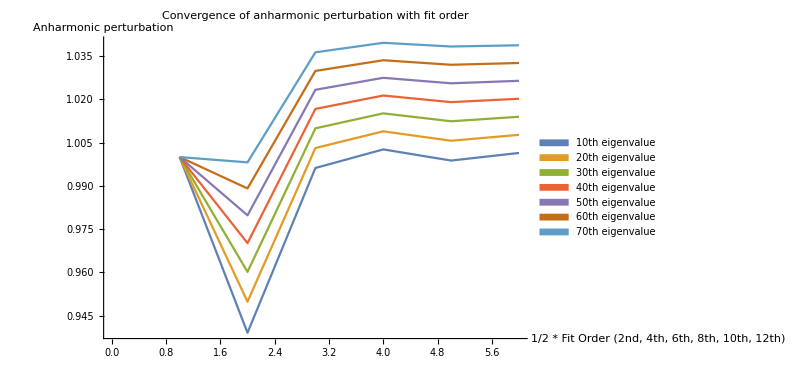

```mathematica
Carbon and zirconium - check convergence of eigenvalues with fit order;
Transpose[relativeEigenval][[70]]
Transpose[relativeEigenvalz][[70]]
plotstuff={ImageSize->600,PlotLegends->SwatchLegend[{"10th eigenvalue","20th eigenvalue","30th eigenvalue","40th eigenvalue","50th eigenvalue","60th eigenvalue","70th eigenvalue"}],PlotLabel->"Convergence of anharmonic perturbation with fit order",AxesLabel->{"1/2 * Fit Order \n(2nd, 4th, 6th, 8th, 10th, 12th)","Anharmonic\nperturbation"}}
ListPlot[Table[Transpose[relativeEigenval][[i]],{i,10,70,10}], Joined->True,plotstuff]
ListPlot[Table[Transpose[relativeEigenvalz][[i]],{i,10,70,10}], Joined->True,plotstuff]
```

```mathematica
Plot input stuff for Carbon eigensystem;
eigenPlots=Table[Show[Plot[Evaluate[(6*eigensysC[[i]][[2]])+eigensysC[[i]][[1]]],{x,-B,B}],Plot[Evaluate@V[1,2i,x],{x,-B,B}],PlotRange->{{-B,B},{0,H}},AxesOrigin->{-B,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
```

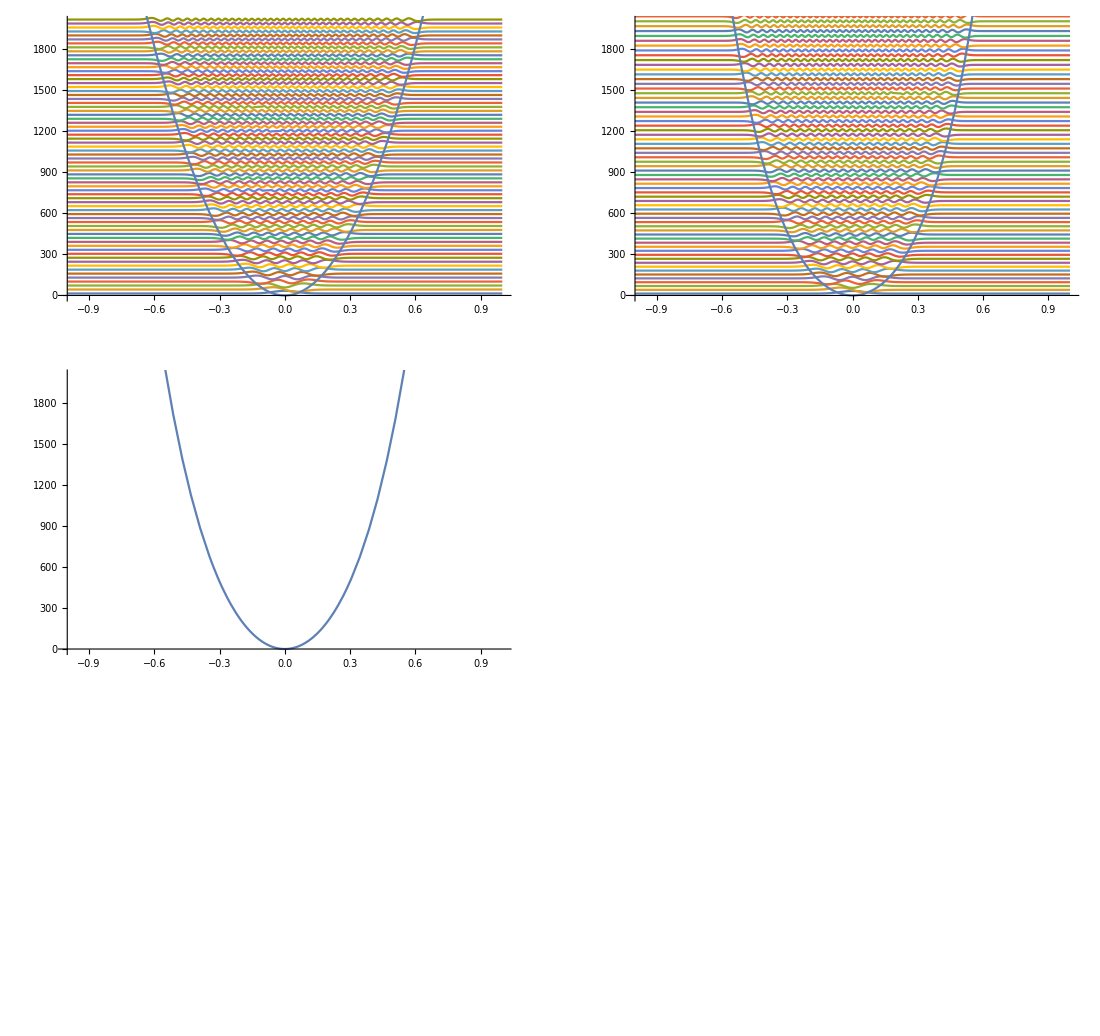

```mathematica
Plot carbon potential and eigensystem (eigenvectors and eigenvectors*eigenvalues);
GraphicsGrid[plotgrid,ImageSize->1100]
```

```mathematica
Plot input stuff for Zr eigensystem;
Bz=0.5;Hz=1000;
eigenPlotsz=Table[Show[Plot[Evaluate[(4*eigensysZ[[i]][[2]])+eigensysZ[[i]][[1]]],{x,-Bz,Bz}],Plot[Evaluate@V[2,2i,x],{x,-Bz,Bz}],PlotRange->{{-Bz,Bz},{0,Hz}},AxesOrigin->{-Bz,0}],{i,1,6}];
plotgrid={Table[eigenPlots[[i]],{i,1,2}],Table[eigenPlots[[j]],{j,3,4}],Table[eigenPlots[[k]],{k,5,6}]};
plotgridz={Table[eigenPlotsz[[i]],{i,1,2}],Table[eigenPlotsz[[j]],{j,3,4}],Table[eigenPlotsz[[k]],{k,5,6}]};
```

```mathematica
Plot zirconium eigensystem;
GraphicsGrid[plotgridz,ImageSize->1100]
```

-Graphics-

```mathematica
Carbon - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1=Fit[relativeEigenval[[5]],{1,x},x]
anharmonicfit2=Fit[relativeEigenval[[5]],{1, x, x^2},x]
anharmonicfit3=Fit[relativeEigenval[[5]],{1, x, x^2,x^3},x]
anharmonicfit4=Fit[relativeEigenval[[5]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ImageSize->900]
```

0.99764+0.00194415 x

0.994767+0.00218355 x-3.37191×10^-6 x^2

0.994724+0.00219055 x-3.61638×10^-6 x^2+2.29548×10^-9 x^3

0.994884+0.00214842 x-9.9042×10^-7 x^2-5.49622×10^-8 x^3+4.03223×10^-10 x^4

-Graphics-

```mathematica
Zirconium - fit an approximate analytic function to the anharmonic perturbation;
(*Make a function of different polynomial orders*)
anharmonicfit1z=Fit[relativeEigenvalz[[6]],{1,x},x]
anharmonicfit2z=Fit[relativeEigenvalz[[6]],{1, x, x^2},x]
anharmonicfit3z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3},x]
anharmonicfit4z=Fit[relativeEigenvalz[[6]],{1, x, x^2,x^3,x^4},x]
Show[ListPlot[relativeEigenvalz[[6]],PlotLabel->"Zirconium anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

Null Zirconium

0.995252+0.000623272 x

0.995172+0.000629912 x-9.35212×10^-8 x^2

0.995239+0.000619062 x+2.85817×10^-7 x^2-3.56186×10^-9 x^3

0.99529+0.000605575 x+1.12654×10^-6 x^2-2.18934×10^-8 x^3+1.29095×10^-10 x^4

-Graphics-

```mathematica
(*Compare C and Zr anharmonic perturbations*)
Show[ListPlot[relativeEigenval[[5]],PlotLabel->"Zirconium and carbon anharmonic pertubation vs eigenvalue \n and 1st, 2nd, 3rd, 4th order fits",AxesLabel->{"Eigenvalue","Anharmonic perturbation"}],Plot[{anharmonicfit1,anharmonicfit4},{x,1,70}],ListPlot[relativeEigenvalz[[6]]],Plot[{anharmonicfit1z,anharmonicfit4z},{x,1,70}],ImageSize->900]
```

-Graphics-

```mathematica
Not finished - continue from here
```

-continue from here+finished Not

```mathematica
(*Plot derivitive of C and Zr anharmonic perturbation fits*)
cAnharmonicityDerivitive=D[{anharmonicfit1,anharmonicfit2,anharmonicfit3,anharmonicfit4},x]
zrAnharmonicityDerivitive=D[{anharmonicfit1z,anharmonicfit2z,anharmonicfit3z,anharmonicfit4z},x]
GraphicsGrid[{{Show@Plot[{cAnharmonicityDerivitive},{x,0,70},ImageSize->400],Show@Plot[{zrAnharmonicityDerivitive},{x,0,70}]}}]
```

{0.00194415,0.00218355-6.74383×10^-6 x,0.00219055-7.23276×10^-6 x+6.88644×10^-9 x^2,0.00214842-1.98084×10^-6 x-1.64887×10^-7 x^2+1.61289×10^-9 x^3}

{0.000623272,0.000629912-1.87042×10^-7 x,0.000619062+5.71634×10^-7 x-1.06856×10^-8 x^2,0.000605575+2.25308×10^-6 x-6.56801×10^-8 x^2+5.16381×10^-10 x^3}

-Graphics-

```mathematica
(*Calculate partition function and Helmholtz free energy with Einstein frequencies*)
(*As previous, define omega0 as the solution to A*x*x=1/2*m*omega*omega*x*x, where A*x*x is the harmonic fit*)
"4.685Ang Einstein frequencies from polynomial fit:"
Acarbon=V[1,2,X][[1]];
cOmega0=Sqrt[2Acarbon/m[[1]]]
Azirconium=V[2,2,X][[1]];
zOmega0=Sqrt[2Azirconium/m[[2]]] 
(*Note, if we define the Einstein frequency in terms of the QHA DOS as the energy integrating up to which gives the number of modes equal to the 3*Natoms/2, then the frequencies are*)
"4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:"
cOmegaInt48=65.1879672429008/2
zrOmegaInt48=26.329538754361874/2
"4.685Ang Einstein frequencies from QHA finding peak frequency for each band:"
cOmegaMaxPeak=4.14*18.0295229515/2
zrOmegaMaxPeak=4.14*6.2446881878/2
```

4.685Ang Einstein frequencies from polynomial fit:

29.0249

12.0836

4.685Ang Einstein frequencies from QHA finding integration limit that gives 48 (3*Natoms/2) for each band:

32.594

13.1648

4.685Ang Einstein frequencies from QHA finding peak frequency for each band:

37.3211

12.9265

```mathematica
(*Zirconium eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergiesZ[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.498031 | 1.49472 | 2.49267 | 3.49188 | 4.49235 | 5.49408 | 6.49706 | 7.50131 | 8.50682 | 9.51358 | 10.5216 | 11.5309 | 12.5414 | 13.5532 | 14.5663
15.5806 | 16.5962 | 17.613 | 18.6311 | 19.6504 | 20.671 | 21.6928 | 22.7159 | 23.7403 | 24.7659 | 25.7927 | 26.8208 | 27.8501 | 28.8807 | 29.9126
30.9456 | 31.98 | 33.0155 | 34.0524 | 35.0904 | 36.1297 | 37.1702 | 38.212 | 39.255 | 40.2993 | 41.3448 | 42.3915 | 43.4394 | 44.4886 | 45.539
46.5906 | 47.6435 | 48.6976 | 49.7529 | 50.8094 | 51.8672 | 52.9262 | 53.9863 | 55.0478 | 56.1104 | 57.1742 | 58.2393 | 59.3056 | 60.373 | 61.4417

```mathematica
(*Carbon eigenspectrum*)
(*Ideal harmonic eigenvalue spectrum*)
perfectHarmonic=Table[0.5+i,{i,0,69}];
Partition[perfectHarmonic,15]//TableForm
(*2nd order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[1]],15]//TableForm
(*12th order fit harmonic eigenvalue spectrum*)
Partition[eigenEnergies[[6]],15]//TableForm
```

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.5 | 1.5 | 2.5 | 3.5 | 4.5 | 5.5 | 6.5 | 7.5 | 8.5 | 9.5 | 10.5 | 11.5 | 12.5 | 13.5 | 14.5
15.5 | 16.5 | 17.5 | 18.5 | 19.5 | 20.5 | 21.5 | 22.5 | 23.5 | 24.5 | 25.5 | 26.5 | 27.5 | 28.5 | 29.5
30.5 | 31.5 | 32.5 | 33.5 | 34.5 | 35.5 | 36.5 | 37.5 | 38.5 | 39.5 | 40.5 | 41.5 | 42.5 | 43.5 | 44.5
45.5 | 46.5 | 47.5 | 48.5 | 49.5 | 50.5 | 51.5 | 52.5 | 53.5 | 54.5 | 55.5 | 56.5 | 57.5 | 58.5 | 59.5

0.498622 | 1.49811 | 2.50206 | 3.51044 | 4.52322 | 5.54037 | 6.56185 | 7.58765 | 8.61772 | 9.65203 | 10.6906 | 11.7333 | 12.7802 | 13.8312 | 14.8863
15.9456 | 17.0088 | 18.0761 | 19.1475 | 20.2227 | 21.302 | 22.3852 | 23.4723 | 24.5633 | 25.6581 | 26.7568 | 27.8594 | 28.9657 | 30.0758 | 31.1896
32.3072 | 33.4285 | 34.5536 | 35.6822 | 36.8146 | 37.9506 | 39.0902 | 40.2334 | 41.3802 | 42.5305 | 43.6844 | 44.8419 | 46.0028 | 47.1673 | 48.3352
49.5066 | 50.6814 | 51.8596 | 53.0413 | 54.2264 | 55.4148 | 56.6066 | 57.8018 | 59.0003 | 60.2021 | 61.4072 | 62.6156 | 63.8273 | 65.0422 | 66.2604

```mathematica
cOmega0*perfectHarmonic
cOmega0*eigenEnergies
```

{14.5125,43.5374,72.5624,101.587,130.612,159.637,188.662,217.687,246.712,275.737,304.762,333.787,362.812,391.837,420.862,449.887,478.912,507.937,536.961,565.986,595.011,624.036,653.061,682.086,711.111,740.136,769.161,798.186,827.211,856.236,885.261,914.286,943.311,972.336,1001.36,1030.39,1059.41,1088.44,1117.46,1146.49,1175.51,1204.54,1233.56,1262.59,1291.61,1320.64,1349.66,1378.68,1407.71,1436.73,1465.76,1494.78,1523.81,1552.83,1581.86,1610.88,1639.91,1668.93,1697.96,1726.98,1756.01,1785.03,1814.06,1843.08,1872.11,1901.13,1930.16,1959.18,1988.21,2017.23}

{{14.5125,43.5374,72.5624,101.587,130.612,159.637,188.662,217.687,246.712,275.737,304.762,333.787,362.812,391.837,420.862,449.887,478.912,507.937,536.961,565.986,595.011,624.036,653.061,682.086,711.111,740.136,769.161,798.186,827.211,856.236,885.261,914.286,943.311,972.336,1001.36,1030.39,1059.41,1088.44,1117.46,1146.49,1175.51,1204.54,1233.56,1262.59,1291.61,1320.64,1349.66,1378.68,1407.71,1436.73,1465.76,1494.78,1523.81,1552.83,1581.86,1610.88,1639.91,1668.93,1697.96,1726.98,1756.01,1785.03,1814.06,1843.08,1872.11,1901.13,1930.16,1959.18,1988.21,2017.23},{13.7017,41.2053,68.9072,96.8037,124.891,153.166,181.624,210.263,239.08,268.071,297.234,326.566,356.065,385.728,415.552,445.536,475.676,505.972,536.42,567.02,597.768,628.663,659.704,690.888,722.213,753.679,785.283,817.024,848.901,880.912,913.055,945.329,977.733,1010.27,1042.93,1075.71,1108.62,1141.65,1174.81,1208.09,1241.49,1275.,1308.64,1342.39,1376.26,1410.24,1444.33,1478.54,1512.87,1547.3,1581.84,1616.49,1651.26,1686.12,1721.1,1756.18,1791.37,1826.66,1862.06,1897.56,1933.16,1968.86,2004.67,2040.57,2076.57,2112.68,2148.88,2185.18,2221.57,2258.06},{14.4247,43.3424,72.3963,101.585,130.907,160.362,189.948,219.664,249.509,279.482,309.581,339.807,370.157,400.631,431.228,461.947,492.787,523.746,554.825,586.022,617.337,648.769,680.316,711.978,743.754,775.644,807.647,839.762,871.988,904.324,936.771,969.326,1001.99,1034.76,1067.64,1100.63,1133.72,1166.92,1200.22,1233.63,1267.13,1300.75,1334.46,1368.28,1402.2,1436.22,1470.34,1504.56,1538.87,1573.29,1607.81,1642.42,1677.13,1711.94,1746.84,1781.84,1816.94,1852.13,1887.41,1922.79,1958.26,1993.83,2029.48,2065.23,2101.08,2137.01,2173.04,2209.15,2245.36,2281.65},{14.4624,43.4532,72.575,101.827,131.208,160.717,190.354,220.116,250.004,280.016,310.152,340.41,370.79,401.291,431.913,462.653,493.512,524.489,555.582,586.792,618.118,649.558,681.112,712.78,744.56,776.452,808.456,840.57,872.794,905.128,937.57,970.12,1002.78,1035.54,1068.41,1101.39,1134.47,1167.66,1200.95,1234.35,1267.84,1301.44,1335.15,1368.95,1402.85,1436.86,1470.96,1505.17,1539.47,1573.87,1608.37,1642.97,1677.67,1712.46,1747.34,1782.33,1817.41,1852.58,1887.85,1923.21,1958.66,1994.21,2029.85,2065.59,2101.42,2137.33,2173.34,2209.44,2245.63,2281.91},{14.4779,43.4979,72.6459,101.921,131.323,160.85,190.503,220.279,250.179,280.201,310.345,340.61,370.996,401.501,432.125,462.867,493.727,524.703,555.796,587.004,618.326,649.763,681.313,712.977,744.752,776.639,808.637,840.745,872.963,905.29,937.726,970.269,1002.92,1035.68,1068.54,1101.51,1134.59,1167.77,1201.05,1234.44,1267.93,1301.52,1335.22,1369.01,1402.91,1436.91,1471.01,1505.21,1539.5,1573.9,1608.39,1642.99,1677.68,1712.46,1747.34,1782.32,1817.4,1852.57,1887.83,1923.19,1958.64,1994.19,2029.83,2065.56,2101.38,2137.3,2173.3,2209.4,2245.59,2281.87},{14.4725,43.4824,72.622,101.89,131.286,160.809,190.457,220.231,250.129,280.15,310.293,340.558,370.944,401.45,432.075,462.819,493.68,524.659,555.754,586.964,618.289,649.729,681.282,712.948,744.726,776.616,808.616,840.727,872.948,905.277,937.715,970.262,1002.91,1035.68,1068.54,1101.51,1134.59,1167.77,1201.06,1234.45,1267.94,1301.53,1335.23,1369.03,1402.93,1436.93,1471.02,1505.22,1539.52,1573.92,1608.41,1643.,1677.69,1712.48,1747.36,1782.34,1817.41,1852.58,1887.85,1923.2,1958.66,1994.2,2029.84,2065.57,2101.39,2137.31,2173.31,2209.41,2245.6,2281.88}}

```mathematica
ListPlot[{eigenEnergies[[6]],eigenEnergiesZ[[6]],Table[i+1/2,{i,0,70}]}]
```

-Graphics-

```mathematica
(*Zero point energies*)

(*QHA 48 mode Einstein oscillators*)
zpeEinstein=HH[0.00001,Einstein4685]
(*QHA *)
zpeQHA4685=thermalData4685[[6]][[1]]
(*Quadratic fit to harmonic Einstein oscillator potential for 4.685*)
1.5*(zOmega0+cOmega0)
```

68.6381

69.6031

61.6628

```mathematica
(*Define discrete harmonic thermodynamic functions - Helmholtz - entropy - Cv*)
K2meV=0.086173324;
HH[T_,Einsteinlist_]:=1.5*(0.5*Total[Einsteinlist]+K2meV*T*Total[Log[1-Exp[-((Einsteinlist)/(K2meV*T))]]])

SS[T_,Einsteinlist_]:=1.5*((1/(2*T))*Total[Einsteinlist*Coth[(Einsteinlist)/(2*K2meV*T)]]-K2meV*Total[Log[2*Sinh[(Einsteinlist)/(2*K2meV*T)]]])

EE[T_,Einsteinlist_]:=1.5*(Total[(Einsteinlist)/2]+Total[1/(Exp[Einsteinlist/(K2meV*T)]-1)])

Cv[T_,Einsteinlist_]:=1.5*Total[K2meV*(((Einsteinlist)/(K2meV*T))^2)*(Exp[Einsteinlist/(K2meV*T)]/((Exp[Einsteinlist/(K2meV*T)]-1)^2))]
```

```mathematica
Define general partition function;
(*Partition function as a power series expansion of eigenspectrum http://www.nyu.edu/classes/tuckerman/stat.mech/lectures/lecture_13/node8.html *)
Z[T_,eigenlist_]:=Exp[-eigenlist/(2*K2meV*T)]*Total[Table[Exp[-eigenlist/(K2meV*T)]^k,{k,0,20}]]

Z1[T_,eigenlist_]:=Exp[-eigenlist/(2*K2meV*T)]*Total[Table[Exp[-(eigenlist+k/10)/(K2meV*T)]^k,{k,0,20}]]

Zgen[T_,order_]:={Total[Exp[-2*zOmega0*eigenEnergiesZ[[order]]/(K2meV*T)]],Total[Exp[-2*cOmega0*eigenEnergies[[order]]/(K2meV*T)]]}
```

```mathematica
Zgen[1,1]
Z[1,einsteinOmega0[[1]]]
```

{1.26341×10^-61,5.25654×10^-147}

1.26341×10^-61

```mathematica
Z[1000,einsteinOmega0]
Zgen[1000,1]
Zgen[1000,6]
```

{3.54423,1.45677}

{3.55407,1.45677}

{3.55431,1.45402}

```mathematica
eigenEnergies[[1]]
cOmega0*2
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5,40.5,41.5,42.5,43.5,44.5,45.5,46.5,47.5,48.5,49.5,50.5,51.5,52.5,53.5,54.5,55.5,56.5,57.5,58.5,59.5,60.5,61.5,62.5,63.5,64.5,65.5,66.5,67.5,68.5,69.5}

58.0499

```mathematica
einsteinOmega0
```

{24.1671,58.0499}

```mathematica
Define free energy of Helmholtz via partition function;
einsteinOmega0=2{zOmega0,cOmega0};
maxEigen=100;
a[T_,eigenlist_]:=-K2meV*1.5T*Log[Z[T,eigenlist]]
a1[T_,eigenlist_]:=-K2meV*1.5*T*Log[Z1[T,eigenlist]]
A[T_,1]:=-K2meV*1.5*T*Log[Zgen[T,1]]
A[T_,6]:=-K2meV*1.5*T*Log[Zgen[T,6]]
(*Perfect Einstein Helmholtz Free energy from partition function*)
Plot[{Total@a[T,einsteinOmega0],Total@A[T,6],Total@a1[T,einsteinOmega0]},{T,1,4000}]
```

-Graphics-

```mathematica
Plot[{A[T,1],Total[a[T,einsteinOmega0]]},{T,1,70}]
```

-Graphics-

```mathematica
Plot[{A[T,1],Total[a[T,einsteinOmega0]]},{T,1,70}]
```

-Graphics-

```mathematica
A[0.00001,6]
A[0.00001,1]
Total[a[0.0001,einsteinOmega0]]
```

{18.054,43.4174}

{18.1253,43.5374}

61.6628

```mathematica
Plot[A[T,1],{T,1,1000}]
Plot[A[T,1]-A[T,6],{T,1,4000}]
Plot[Evaluate@{-t*A'[t,1],-t*A'[t,6]}/.t->T,{T,1,1000},PlotRange->{{0,1000},{-1,100}}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
{-t*A'[t,1],-t*A'[t,6]}/.t->1000000
```

{-1000000 A'[1000000,1],-1000000 A'[1000000,6]}

```mathematica
Plot[{-t*A'[t,1]+t*A'[t,6]}/.t->T,{T,1,1000},PlotRange->{{0,1000},{-0.00001,0.00001}}]
```

-Graphics-

```mathematica
f
```

f

```mathematica
Plot[{-T*A''[T,1]+T*A''[T,6]}/.T->t,{t,300,4000},PlotRange->All]
Plot[{-T*A''[T,1],-T*A''[T,6]}/.T->t,{t,300,4000},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Define entropy via partition function;
(*Entropy is the first derivative of A wrt T*)
S[T_,LIST_]:=-1.5D[a[t,einsteinOmega0],t]/.t->T
Plot[{S[T,einsteinOmega0],Total[S[T,einsteinOmega0]]},{T,1,4000}]
```

-Graphics-

```mathematica
Define heat capacity via partition function;
(*Heat capacity is the - second derivative of A wrt T times T*)
Cv[T_,LIST_]:=-1.5*t*D[D[a[t,einsteinOmega0],t],t]/.t->T
Plot[{Cv[T,einsteinOmega0],Total[Cv[T,einsteinOmega0]]},{T,100,4000}]
```

-Graphics-

```mathematica
Cv[100,einsteinOmega0]
```

100 S'[100,{24.1671,58.0499}]